```mathematica
RuleIntToDigits[{n_, k_, r_}] := {IntegerDigits[n, k,k^(2r+1)],k,r}
RuleDigitsToInt[{ruleDigits_, k_, r_}] := Module[{total=0},For[i=0,i<Length[ruleDigits], i++,total+=ruleDigits[[k^(2r+1)-i]]*(k^i)];{total,k,r}]
```

```mathematica
RandomRuleMutation[{ruleDigits_, k_, r_}] :=
With[
{pos=RandomInteger[{1, k^(2r+1)}]},
{ReplacePart[ruleDigits,pos->Mod[ruleDigits[[pos]]+RandomInteger[{1, k-1}],k]],k,r}]
```

```mathematica
RuleDifference[{ruleDigits1_,ruleDigits2_}] := Position[MapThread[Unequal,{ruleDigits1,ruleDigits2}],True]//Flatten
RuleDifferences[rules_List] := Map[RuleDifference, Partition[rules,2,1]]
GridArrows[positions_]:=Join[{Arrowheads[0.02]}, Map[Arrow[{{#-.5,2},{#-.5,1}}]&,positions]]
RulesMutationPlot[rules_List] :=
With[{rulesDigits=First/@rules},
GraphicsColumn[Join[
{ArrayPlot[{First@rulesDigits}, Mesh->True,PlotRangePadding->{{0,0},{0,1}}]},
MapThread[
ArrayPlot[{#1}, Mesh->True,Epilog->GridArrows[#2], PlotRangePadding->{{0,0},{0,1}}]&,
{Rest[rulesDigits],RuleDifferences[rulesDigits]}
]
], Center, 0]]
```

```mathematica
CALifetime[{ruleDigits_,k_,r_}, cutoff_] := With[{rule=RuleDigitsToInt[{ruleDigits,k,r}]},
NestWhileList[
CellularAutomaton[rule,#]&,
CenterArray[cutoff*2+1],
Max[#]!=0&,
1, cutoff
] // Length] // If[#==cutoff+1, Infinity, #]&
```

```mathematica
initialRule=RuleIntToDigits[{0,3,1}];
```

```mathematica
ruleLifetimes=Module[{rule,lifetime, cutoff=200},
NestList[CompoundExpression[
rule=RandomRuleMutation[First[#]],
lifetime=CALifetime[rule, cutoff],
If[lifetime>=Last[#] && lifetime != Infinity, {rule, lifetime}, #]
]&, {initialRule, 0}, 10000]
];
```

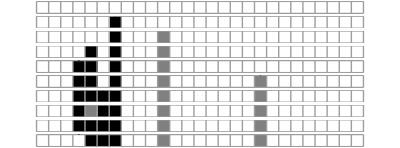

```mathematica
RulesMutationPlot[(First/@Split[First/@ruleLifetimes])[[;;10]]]
```

```mathematica
changedRules=First/@SplitBy[ruleLifetimes,Last];
```

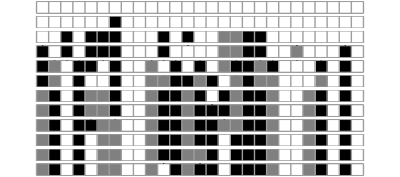

```mathematica
RulesMutationPlot[First/@changedRules]
```

```mathematica
caRules=RuleDigitsToInt/@First/@changedRules;
lifetimes=Last/@changedRules;
```


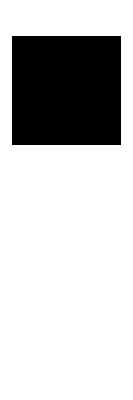
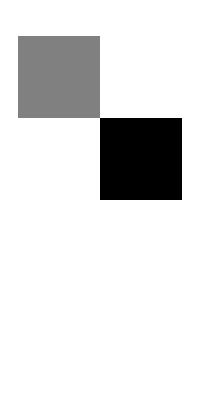
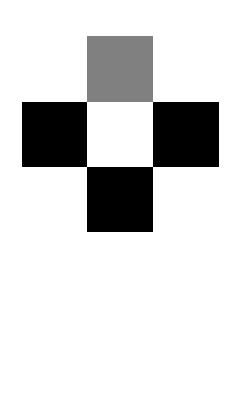
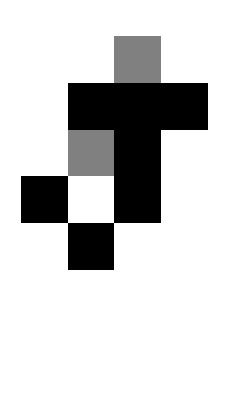
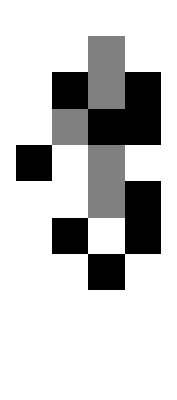
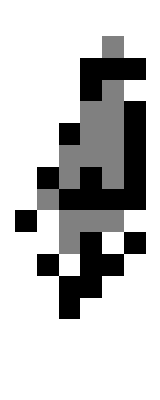
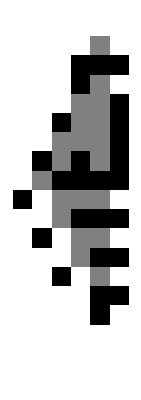
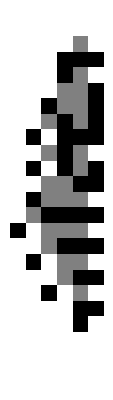

```mathematica
ArrayPlot/@MapThread[
CellularAutomaton[#1, {{1},0},#2]&,
{caRules,lifetimes}]
```

```mathematica
UndirectedGraph[Catenate[Table[#->MapAt[1-#&,#,i],{i,Length[#]}]&/@Tuples[{1,0},7]],EdgeStyle->Opacity[.4,Gray],VertexSize->0,VertexLabels->{x_:>Placed[ArrayPlot[{Append[x,0]},
Mesh->True,ImageSize->40],Center]}]
```

-Graphics-

```mathematica
ArrayPlot[{#},Mesh->True]&/@Tuples[{0,1},8]//Column
```

```mathematica
Table[#->MapAt[1-#&,#,i],{i,Length[#]}]&/@Tuples[{1,0},8]//First
```

{{1,1,1,1,1,1,1,1}→{0,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}→{1,0,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}→{1,1,0,1,1,1,1,1},{1,1,1,1,1,1,1,1}→{1,1,1,0,1,1,1,1},{1,1,1,1,1,1,1,1}→{1,1,1,1,0,1,1,1},{1,1,1,1,1,1,1,1}→{1,1,1,1,1,0,1,1},{1,1,1,1,1,1,1,1}→{1,1,1,1,1,1,0,1},{1,1,1,1,1,1,1,1}→{1,1,1,1,1,1,1,0}}

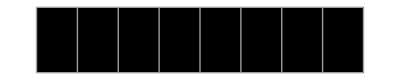
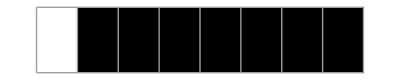
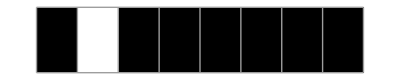
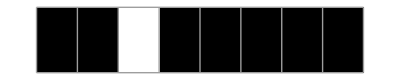
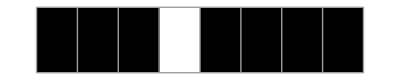
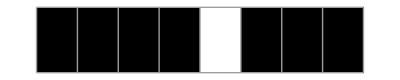
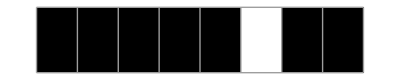
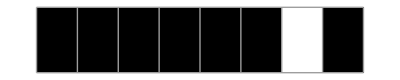
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-

```mathematica
Replace[
Table[#->MapAt[1-#&,#,i],{i,Length[#]}]&/@Tuples[{1,0},8]//First, 
x_List:>ArrayPlot[{x},Mesh->True], 
{2}
]//Column
```

```mathematica
UndirectedGraph[
Catenate[Table[#->MapAt[1-#&,#,i],{i,Length[#]}]&/@Tuples[{1,0},8]],
VertexLabels->{x_:>Placed[ArrayPlot[{x},Mesh->True,ImageSize->40],Center]},
VertexSize->0, EdgeStyle->Opacity[.4,Gray],
ImageSize->500
]
```

-Graphics-